```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
r1=100;
r2=50;
fc=2000;
α=0.7;
c=1×10^-10;
R[f_]:=1/(1/r1+1/(r2+1/(ⅈ 2π f c)));
rc[f_]:=r2+(r1-r2)/(1+(ⅈ f/fc)^α);
(*Admittance*)
fY[f_]:=1/rc[f];

px=(r1+r2)/2
py=-(r1-r2)/(2 Tan[π*α/2])
rr=(r1-r2)/(2Sin[π* α/2])
```

75

-12.7381

28.0582

```mathematica
Plot[Abs[rc[f]],{f,10^2,10^5}];
```

```mathematica
LogLogPlot[{Re[rc[f]],Im[rc[f]]},{f,10^1,10^5}];
```

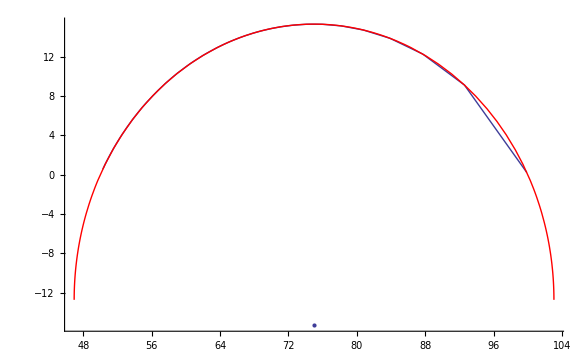

```mathematica
Show[ListPlot[{{Re[rc[fc]],Im[rc[fc]]}}],ParametricPlot[{Re[rc[f]],-Im[rc[f]]},{f,10^0,10^6},AxesLabel->{"R","X"}],ParametricPlot[{rr Cos[th*π/180]+px,rr Sin[th*π/180]+py},{th,0,180},PlotStyle->{Red}],PlotRange->{{40,110},{20,5}}]
```

```mathematica
Plot[Arg[1/rc[f]]/π,{f,10^-2,10^7/2}];
```

```mathematica
(*=============compare data plot and the fitted circle=================*)
```

```mathematica
Needs["PlotLegends`"];

<<BISfit`
Names["BISfit`*"]
```

ColeP::shdw: Symbol ColeP appears in multiple contexts BISfit`Notebook$$31`; definitions in context BISfit` may shadow or be shadowed by other definitions.

{BISLSfit,ColeP,Filterd,Maxd,Mind}

```mathematica
(*data=Import["E:\\work\\thesis\\论文\\标定后的数据\\calib_50.dat","Data"];*)
data=Import["calib_50.dat","Data"];
```

```mathematica
data0=data[[All,{5,6}]];

{m,n,r}=ColeP[data0];
```

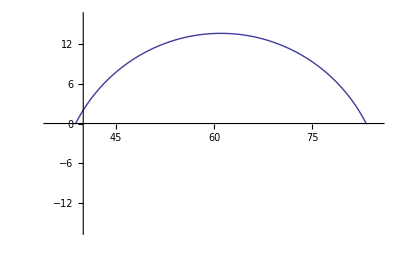

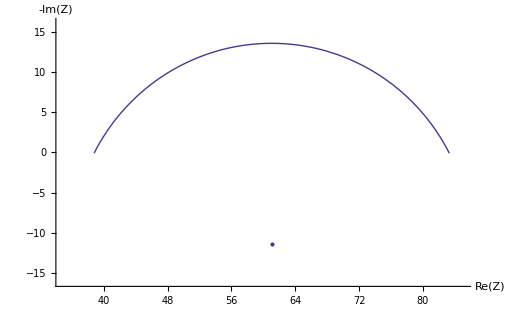

```mathematica
p1=ParametricPlot[{r Cos[th]+m,r Sin[th]+n},{th,π/2-1.1,π/2+1.1},PlotRange->{{35,85},{-16,16}}]
op=ListPlot[{{m,n}},PlotRange->{{35,85},{-16,16}}];
Show[op,p1,AxesLabel->{"Re(Z)","-Im(Z)"}(*,AxesOrigin->{42,0}*)]
```

```mathematica
X=Map[ Function[x,x[[1]]Cos[-x[[2]]π/(180)]],data0];
Y=Map[ Function[x,x[[1]]Sin[-x[[2]]π/(180)]],data0];
Z=Table[{X[[i]],Y[[i]]},{i,Length[X]}];
p2=ListPlot[Z,Joined->True,Mesh->Full,MeshStyle->PointSize[Medium](*,PlotLegend->{"sine"}*)];
(*Legended[p1,"xx"]*)
```

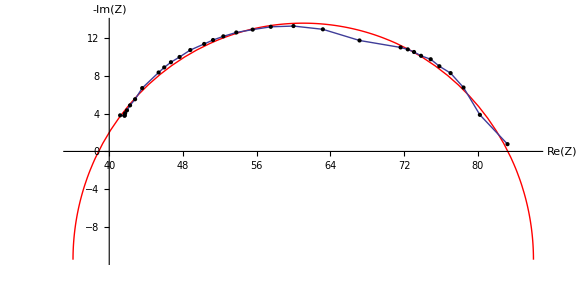

```mathematica
Show[p1,p2,AxesLabel->{"Re(Z)","-Im(Z)"}]
```

38.8401+44.4306/(1+0.00231911 (ⅈ f)^0.697346)

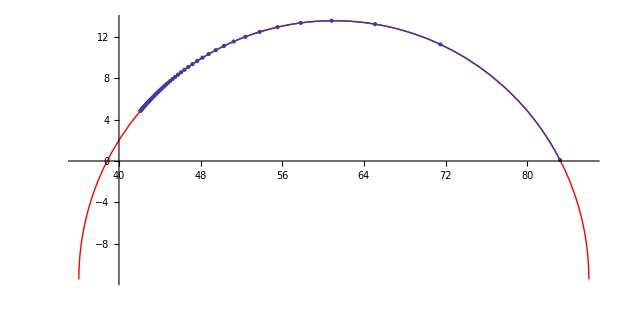

```mathematica
(*now find the cole p*)
{r1,r2,α}=BISLSfit[data0];
rc[f]
p3=ParametricPlot[{Re[rc[f]],-Im[rc[f]]},{f,10^0,10^5},PlotRange->{{30,90},{0,20}},AxesLabel->{"R","X"},Mesh->Full];
Show[{p1,p3}]
```

```mathematica
(* what about Admittance?*)
fY[f]
```

1/(50+50/(1+0.00226618 (ⅈ f)^0.7))

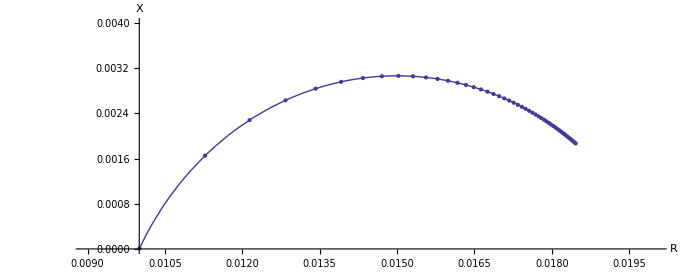

```mathematica
ParametricPlot[{Re[fY[f]],Im[fY[f]]},{f,10^0,10^5},PlotRange->{{0.009,0.02},{0,0.004}},AxesLabel->{"R","X"},Mesh->Full]
```